13.61 | 12.11 | 12.67 | 15.06
11.89 | 13.11 | 13.22 | 10.72
10.89 | 12.39 | 10.61 | 11.61
7.72 | 10.33 | 13.06 | 11.22
8.28 | 8.78 | 10.78 | 12.72
12.44 | 12.44 | 12.72 | 12.61
13.33 | 12.28 | 11.33 | 11.06

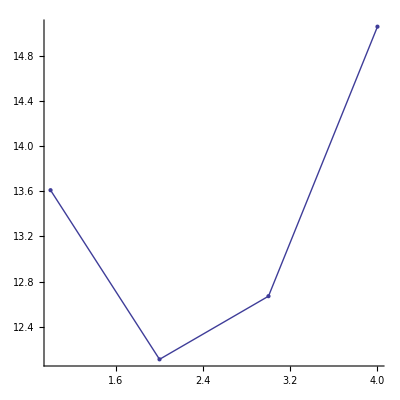
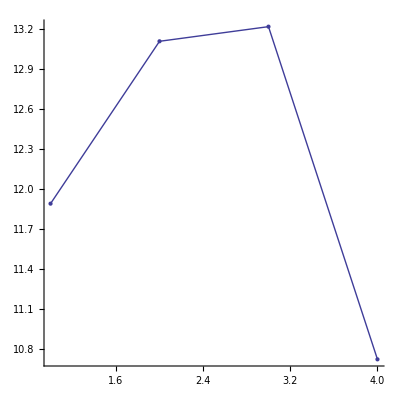
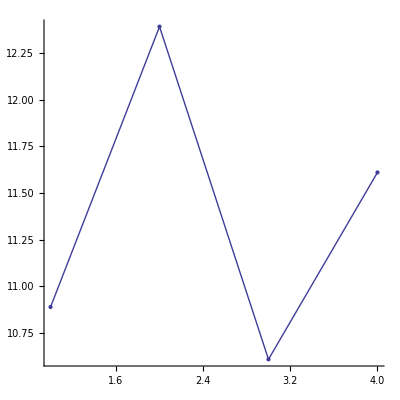
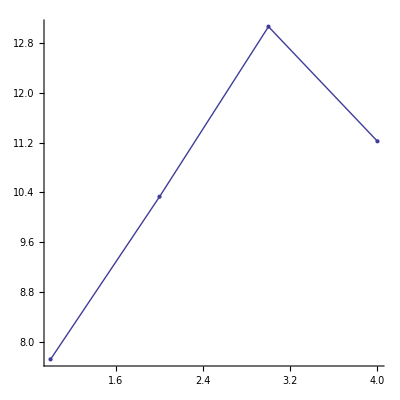
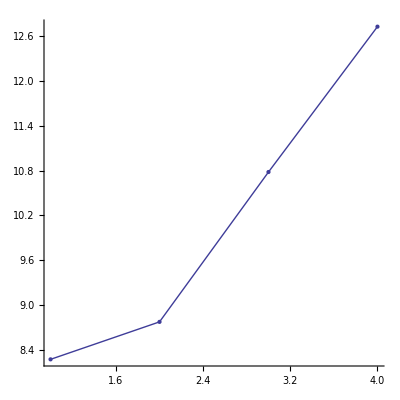
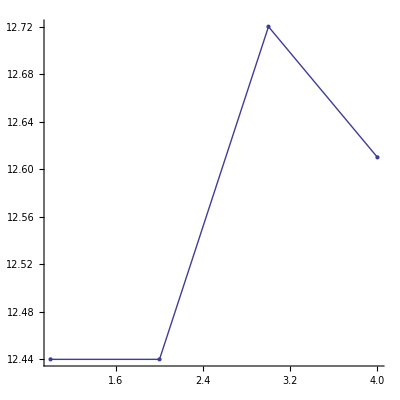
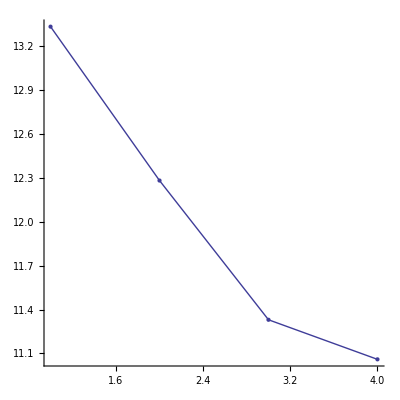

```mathematica
Remove["Global`*"]
weath=WeatherData["Seattle","Temperature",{{#,10,11},{#,10,14},"Day"},"Value"]&/@Table[i,{i,2005,2011}];
TableForm[weath]
Table[ListPlot[weath[[i]],Joined->True,PlotRange->All, PlotStyle->Thick,Mesh->All, AspectRatio->1],{i,1,7}]
(*lm=LinearModelFit[weath,x,x]
p:=ListPlot[weath,Joined->True]
p2:=ListPlot[lm["PredictedResponse"],Joined->True,PlotStyle->Red]
Show[p,p2]
*)
```

```mathematica
WeatherData["Seattle"]
```

AN628

```mathematica
2011-73
```

1938

```mathematica
WeatherData["Santa Clarita","Temperature"]
```

Missing[NotApplicable]